All the following functions are the same as that in CompleteGenericMatrices1D.nb. We will just be using different basis functions.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
colorlist={Black,Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# Core routines

## Project individual tensors

The following function develos the projector for tensors of a particular degree

### From Manuel

```mathematica
ProjectTensor[degree_,nx_,ny_]:=Module[{result,n20,n02,n11,n30,n21,n12,n03,n40,n31,n22,n13,n04,n50,
n41,n32,n23,n14,n05,n60,n51,n42,n33,n24,n15,n06,n70,n61,n52,n43,n34,n25,n16,n07},

n20=nx*nx;n02=ny*ny;n11=nx*ny;

n30=nx*n20;n21=ny*n20;n12=ny*n11;n03=ny*n02;

n40=nx*n30;n31=ny*n30;n22=nx*n12;n13=nx*n03;n04=ny*n03;

n50=nx*n40;
n41=ny*n40;n32=nx*n22;n23=nx*n13;n14=ny*n13;n05=ny*n04;

n60=nx*n50;n51=ny*n50;n42=nx*n32;n33=nx*n23;n24=ny*n23;n15=ny*n14;n06=ny*n05;


n70=nx*n60;n61=ny*n60;n52=nx*n42;n43=nx*n33;n34=ny*n33;n25=ny*n24;n16=ny*n15;n07=ny*n06;


Which[degree == 0,
result = {1},
degree == 1,
result = {nx,ny,-ny,nx};
result=ArrayReshape[result,{2,2}];,
degree == 2,
result = {nx*nx,2*nx*ny,ny*ny,-nx*ny,nx*nx-ny*ny,nx*ny,ny*ny,-2*nx*ny,nx*nx};
result=ArrayReshape[result,{3,3}];,
degree == 3,
result = {nx*nx*nx,3*ny*nx*nx,3*nx*ny*ny,ny*ny*ny,-ny*nx*nx,nx*nx*nx-2*nx*ny*ny,2*ny*nx*nx-ny*ny*ny,nx*ny*ny,nx*ny*ny,-2*ny*nx*nx+ny*ny*ny,nx*nx*nx-2*nx*ny*ny,ny*nx*nx,-ny*ny*ny,3*nx*ny*ny,-3*ny*nx*nx,nx*nx*nx};
result=ArrayReshape[result,{4,4}];,
degree ==4,
result = {n40,4*n31,6*n22,4*n13,n04,-n31,-3*n22+n40,-3*n13+3*n31,-n04+3*n22,n13,n22,2*n13-2*n31,n04-4*n22+n40,-2*n13+2*n31,n22,-n13,-n04+3*n22,3*n13-3*n31,-3*n22+n40,n31,n04,-4*n13,6*n22,-4*n31,n40};

result = ArrayReshape[result,{degree+1,degree+1}];,
degree == 5,
result = {n50,5*n41,10*n32,10*n23,5*n14,n05,-n41,-4*n32+n50,-6*n23+4*n41,-4*n14+6*n32,-n05+4*n23,n14,n32,3*n23-2*n41,3*n14-6*n32+n50,n05-6*n23+3*n41,-2*n14+3*n32,n23,-n23,-2*n14+3*n32,-n05+6*n23-3*n41,3*n14-6*n32+n50,-3*n23+2*n41,n32,n14,n05-4*n23,-4*n14+6*n32,6*n23-4*n41,-4*n32+n50,n41,-n05,5*n14,-10*n23,10*n32,-5*n41,n50};

result=ArrayReshape[result,{degree+1,degree+1}];,
degree==6,
result = {n60,6*n51,15*n42,20*n33,15*n24,6*n15,n06,-n51,-5*n42+n60,-10*n33+5*n51,-10*n24+10*n42,-5*n15+10*n33,-n06+5*n24,n15,n42,4*n33-2*n51,6*n24-8*n42+n60,4*n15-12*n33+4*n51,n06-8*n24+6*n42,-2*n15+4*n33,n24,-n33,-3*n24+3*n42,-3*n15+9*n33-3*n51,-n06+9*n24-9*n42+n60,3*n15-9*n33+3*n51,-3*n24+3*n42,n33,n24,2*n15-4*n33,n06-8*n24+6*n42,-4*n15+12*n33-4*n51,6*n24-8*n42+n60,-4*n33+2*n51,n42,-n15,-n06+5*n24,5*n15-10*n33,-10*n24+10*n42,10*n33-5*n51,-5*n42+n60,n51,n06,-6*n15,15*n24,-20*n33,15*n42,-6*n51,n60};

result=ArrayReshape[result,{degree+1,degree+1}];,
degree == 7,
result = {n70,7*n61,21*n52,35*n43,35*n34,21*n25,7*n16,n07,-n61,-6*n52+n70,-15*n43+6*n61,-20*n34+15*n52,-15*n25+20*n43,-6*n16+15*n34,-n07+6*n25,n16,n52,5*n43-2*n61,10*n34-10*n52+n70,10*n25-20*n43+5*n61,5*n16-20*n34+10*n52,n07-10*n25+10*n43,-2*n16+5*n34,n25,-n43,-4*n34+3*n52,-6*n25+12*n43-3*n61,-4*n16+18*n34-12*n52+n70,-n07+12*n25-18*n43+4*n61,3*n16-12*n34+6*n52,-3*n25+4*n43,n34,n34,3*n25-4*n43,3*n16-12*n34+6*n52,n07-12*n25+18*n43-4*n61,-4*n16+18*n34-12*n52+n70,6*n25-12*n43+3*n61,-4*n34+3*n52,n43,-n25,-2*n16+5*n34,-n07+10*n25-10*n43,5*n16-20*n34+10*n52,-10*n25+20*n43-5*n61,10*n34-10*n52+n70,-5*n43+2*n61,n52,n16,n07-6*n25,-6*n16+15*n34,15*n25-20*n43,-20*n34+15*n52,15*n43-6*n61,-6*n52+n70,n61,-n07,7*n16,-21*n25,35*n34,-35*n43,21*n52,-7*n61,n70};

result=ArrayReshape[result,{degree+1,degree+1}];
];


result
]
```

### General Routine

```mathematica
ProjectorGeneral2D[deg_]:=Module[{result,project1,I,size,normalizer},
(*Projector for the first order tensor*)
project1 = {{nx,ny},{-ny,nx}};
result = 0;

If[deg==0,result = 1,result = project1;
Do[
size = Length[result];
result=KroneckerProduct[project1,result];

(*now we contract the result*)
I = ConstantArray[0,{Length[result],ii+1}];
I⟦1;;size,1;;size⟧=IdentityMatrix[size];
I⟦(size+1);;-1,-size;;-1⟧=IdentityMatrix[size];

result = Transpose[I].result.I;

 ,{ii,2,deg}];

(*extract the first coloumn of result*)
normalizer=Abs[result⟦All,1⟧/.{nx->1,ny->1}];

result =Simplify[Inverse[DiagonalMatrix[normalizer]].result];

];



result

]
```

### Check

```mathematica
Simplify[ProjectTensor[2,nx,ny]-ProjectorGeneral2D[2]]

Simplify[ProjectTensor[3,nx,ny]-ProjectorGeneral2D[3]]

Simplify[ProjectTensor[4,nx,ny]-ProjectorGeneral2D[4]]

Simplify[ProjectTensor[5,nx,ny]-ProjectorGeneral2D[5]]

Simplify[ProjectTensor[6,nx,ny]-ProjectorGeneral2D[6]]

Simplify[ProjectTensor[7,nx,ny]-ProjectorGeneral2D[7]]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

## Assemble General

```mathematica
(*Assemble a general matrix for 2D computations*)
Assemble2D[Ntensors_,Routine_]:=Module[{size,result,locDiagonal,numVar,deg},

(*degrees of different tensors*)
deg = Table[iTensorDegree[ii],{ii,1,Ntensors}];

(*size corresponding to every tensor degree*)
size=Table[Length[Pick[IDXtrf[deg[[i]]],Flatten[Join[{1},Table[{1,0},{k,1,deg[[i]]}]]],1]],{i,1,Ntensors}];

(*Total number of variables*)
numVar = Total[size];

(*location at the diagonal for the symmetrizer*)
locDiagonal = Flatten[ConstantArray[0,{1,Length[size]+1}]];
locDiagonal[[1]] =1;
Do[locDiagonal[[ii+1]]+=locDiagonal[[ii]]+size[[ii]],{ii,1,Length[size]}];

result = ConstantArray[0,{numVar,numVar}];

Do[
result⟦Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1],Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1]⟧=Routine[deg[[ii]]],{ii,1,Length[size]}];

result
]
```

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity2[a_,filename_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]]-1,{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]]-1,{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["../system_matrices/",filename]];

WriteString[str,ToString[nnz],"\n"];

Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
(*Minus 1 to take care of the C indices*)
Do[WriteString[str,ToString[vec[[ii]]-1],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Basic Definitions

```mathematica
(*ref to manuels paper on fluxes for large moment system for a detailed expression*)
(*total tensorial degree including traces*)
iFullDegree[i_]=Floor[√(4i-3)-1];
(*number of traces C^2 has one trace*)
iTraces[i_]=Floor[(1+1/2 iFullDegree[i])^2]-i;
(*actual tensorial degree*)
iTensorDegree[i_]=iFullDegree[i]-2iTraces[i];
ii[s_,A_]=Floor[(A+2(s+1))/2](A+2(s+1)-Floor[(A+2(s+1))/2])-s;

(*i is as defined in the reference*)
NumberOfVariables2D[ntensors_]:=Sum[iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfVariables3D[ntensors_]:=Sum[2iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfFullTensors3D[ntensors_]:=Block[{m=iFullDegree[ntensors],frac},
m-(((m+1)(m+2)(m+3))/6.-Sum[2iTensorDegree[i]+1,{i,1,ntensors}])/(((m+1)(m+2))/2)
];

varName[s_,ix_,iy_,iz_]:=StringJoin["ρ",ToString[s],ConstantArray["x",ix],ConstantArray["y",iy],ConstantArray["z",iz]]


(*this is not the norm of ψ, rather it's the norm of the laguerre polynomials*)
Normψ[a_,deg_]=(deg!a!Gamma[deg+a+3/2])/Gamma[deg+3/2];

(*given a tensor W extract all the independed components in 2D in case of trace free situation*)
trfComponents2D[W_]:=Extract[W,Map[Position[IDX[TensorDegree[W]],#]⟦1⟧&,Pick[IDXtrf[TensorDegree[W]],Flatten[Join[{1},Table[{1,0},{k,1,TensorDegree[W]}]]],1]]]


trfVar2D[deg_,name_]:=Table[name[i],{i,1,deg+1}]
From2Dto3D[list_]:=Flatten[Join[{list⟦1⟧},Table[{list⟦k⟧,0},{k,2,Length[list]}]]]


R2[0,1]={{1},{0}};
R2[0,2]={{0},{1}};

Do[
(*Given the components of a tensor represented by B, then tmp collects the terms corresponding to \partial_x in \partial_<x_{in} w_{i1..in>}
the second one does the same job but for a tensor product. *)
tmp=Normal[CoefficientArrays[trfComponents2D[SymDot2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]],{dx,dy}]]⟦2⟧;
(*store the coefficient infront of the moments*)
Do[R1[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];

(*same as above but for tensor products*)
tmp=Normal[CoefficientArrays[trfComponents2D[SymTracefree[SymProduct2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]]],{dx,dy}]]⟦2⟧;
(*store the coefficients infront of the moments*)
Do[R2[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];
,{d,1,15}];

(*The following is the main moment equation*)
recursion1[a_,deg_,flag_]:=(
√((2 deg+2)/(2deg+3))(√(deg+a+3/2)R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a,deg+1]&]-√a R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a-1,deg+1]&])
+If[deg>0,√((2deg)/(2deg+1))(√(deg+a+1/2)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a,deg-1]&]-√(a+1)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a+1,deg-1]&]),0])

(*(Give two Laguerre polynomials Subscript[(L^(n)), a] and Subscript[(L^(m)), b] then the following routine computes (∫^∞)_0 Subscript[(L^(n)(x^2/2)), a](L^(m)(x^2/2))))_b x^2 ⅇ^(-x^2/2)dx. Uses the Laguerre polynomials used in file CompleteGenericMatrices1D.nb*)
mixed[a_,n_,b_,m_]:=Expand[Sum[Binomial[n-(n+m)/2+a-c1-1,a-c1](a!)/(c1!)Binomial[m-(n+m)/2+b-c1-1,b-c1](b!)/(c1!)(c1!√2 Gamma[(n+m)/2+c1+3/2] 2^((n+m)/2)),{c1,0,Min[a,b]}]];

(*ratio between the new and old laguerre polynomials*)
factorLaguerre[a_,n_]:=√(Gamma[n+3/2]/(n!a!Gamma[n+a+3/2]));

(*Same as above but for Laguerre polynomials used in the Boundary Value problem paper*)
mixed2[a_,n_,b_,m_]:=Expand[mixed[a,n,b,m]factorLaguerre[a,n]factorLaguerre[b,m]];

(*The following function integrates expressions of the kind ∫νx^m νy^p νz^n dν but the integration is such that only νx >0. Making the transformation to spherical coordinates i.e. νx = Sin ν Cos θ, νy = Sin ν Sin θ and νz = Cos ν we have (∫^(+π/2))_(-π/2)(∫_0)^π(Sinν^(mm+nn+1)Cosν^pp Sinθ^nn Cosθ^mm)dνdθ*)

IntegrateHalfNxNyNz1[ex_]:=Block[{pos1,pos2,pos3,mm=0,nn=0,pp=0,res,res1=νx νy νz ex},
pos1=Position[res1,νx^_];
pos2=Position[res1,νy^_];
pos3=Position[res1,νz^_];
If[Length[pos1]>0,mm=Extract[res1,pos1⟦1⟧]⟦2⟧-1];
If[Length[pos2]>0,nn=Extract[res1,pos2⟦1⟧]⟦2⟧-1];
If[Length[pos3]>0,pp=Extract[res1,pos3⟦1⟧]⟦2⟧-1];
res=Delete[res1,Join[pos1,pos2,pos3]]If[OddQ[nn]||OddQ[pp],0,2π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];
If[Length[pos1]==0,res=res/νx];
If[Length[pos2]==0,res=res/νy];
If[Length[pos3]==0,res=res/νz];
res
]

(*applies integrate halfnxnynz1 to a long expression*)
IntegrateHalfNxNyNz[ex_]:=If[Head[ex]=== Plus,
Apply[Plus,Table[IntegrateHalfNxNyNz1[ex⟦ii⟧],{ii,1,Length[ex]}]],
IntegrateHalfNxNyNz1[ex]]


(*The input of the following function i.e idx1 and idx2 are arrays such that idx1[[{2,3,4}]] = {#xcomponents,#ycomponents,#zcomponents}. The following function computes the half integrals of the form ∫ ψ fdc where ψ is the basis function and the integral is only over the half space. The ψ is represented by one of the input parameters and the basis functions in f are represented by one of the input parameters.

idx1 = index for the testfunction
	   ix2 = index for the basis of the distribution function*)

HalfIntegrate[idx1_,idx2_]:=Block[{Int1,Int2,deg1=Total[idx1⟦{2,3,4}⟧],deg2=Total[idx2⟦{2,3,4}⟧],f0},

(*The following term develops terms of the form ν_(<x^m y^n>). The algorithm is as follows
1. Extract the total number of free indices in the tensor
2. Develop the full sym trace free tensor i.e develop all the components of ν_(<i_(1...)Subscript[i, n]>)
3. Extract the component corresponding to idx1*)

Int1=Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg1]]]⟦toIDX2[idx1⟦{2,3,4}⟧]⟧];

(*Let us consider the part of the distribution function which comes from Rij. This part will be of the form Rxx...+Rzz.... But Rzz = -Rxx-Ryy and therefore Int2 is not simply the tensorised ν_(<x^m y^n>)*)
Int2=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg2]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx2⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg2]]]];
f0= 1/(2 π)^(3/2);

Expand[mixed2[idx1⟦1⟧,deg1,idx2⟦1⟧,deg2]f0 IntegrateHalfNxNyNz[Expand[Int1 Int2]]]
]
```

## Mapping to Conventional Variables

```mathematica
MappingToConventional[Ntensors_]:=Module[{varIdx,varIdxComplete,conVar,resultGas,Var,resultWall},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXtrf but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

(*Conventional Variables for comparison*)
conVar = {ρ,vx,vy,-√(3/2) θ,σxx/(√2),σxy/(√2),σyy/(√2),-√(2/5)qx,-√(2/5)qy,mxxx/(√6),mxxy/(√6),mxyy/(√6),myyy/(√6),Δ/(2 √30),-Rxx/(2 √7),-Rxy/(2 √7),-Ryy/(2 √7),φxxxx/(2 √6),φxxxy/(2 √6),φxxyy/(2 √6),φxyyy/(2 √6),φyyyy/(2 √6),Ωx/(2 √70),Ωy/(2 √70),-ψxxx/(6 √3),-ψxxy/(6 √3),-ψxyy/(6 √3),-ψyyy/(6 √3)};

Var = Map[Apply[w,#]&,varIdxComplete];

resultGas=Table[Var[[ii]]->conVar[[ii]],{ii,1,Length[Var]}];

resultWall = {Subscript[w, wall][0,0,0,0]->ρW,Subscript[w, wall][1,0,0,0]->-√(3/2) θW};

Flatten[{resultGas,resultWall}]
]

conversionMatrixG26 = DiagonalMatrix[{1,1,1,-√(3/2) ,1/(√2),1/(√2),1/(√2),-√(2/5),-√(2/5),1/(√6),1/(√6),1/(√6),1/(√6),1/(2 √30),-1/(2 √7),-1/(2 √7),-1/(2 √7)}];


conversionMatrixG45 = DiagonalMatrix[{1,1,1,-√(3/2),1/(√2),1/(√2),1/(√2),-√(2/5),-√(2/5),1/(√6),1/(√6),1/(√6),1/(√6),1/(2 √30),-1/(2 √7),-1/(2 √7),-1/(2 √7),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √70),1/(2 √70),-1/(6 √3),-1/(6 √3),-1/(6 √3),-1/(6 √3)}];

varConventional26 = {ρ,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy};

varConventional45 = {ρ,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy,φxxxx,φxxxy,φxxyy,φxyyy,φyyyy,Ωx,Ωy,ψxxx,ψxxy,ψxyy,ψyyy};
```

## Matrices generation

### System Matrices

```mathematica
GetMatrices2D[Ntensors_]:=Block[{varIdx,varIdxComplete,theory,normMatrix,varNames,var,Ax,Ay,
var1D,BCvar,varOdd,varIdxCompleteEven,varEven,BCraw,ρindex=1,vindex=2,ρWeqn,BCnum,BCrhs,Praw,BCraw2,varIdxCompleteOdd,IntGasEven,IntGasOdd,varIdxWall,IntWall,B,eqnVelocity},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXtrf but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

(*variables for the wall. Density and Temperature*)
varIdxWall = {{0,0,0,0},{1,0,0,0}};

(*computes the number of traces for a given iTensorDegree. The final result gives us the tuple discussed in the paper on the convergence of the boundary value problem.*)
theory=Table[Count[varIdx,{_,k}],{k,0,iFullDegree[Ntensors]}];
(*Print["number of different tensor degrees: ",theory];
Print["corresponding variables (traces,indices): ",Flatten[Table[Table[{a,n-1},{a,0,theory⟦n⟧-1}],{n,1,Length[theory]}],1]];
Print["Number of Variables 1D: ",Ntensors];
Print["Number of Variables 2D: ",NumberOfVariables2D[Ntensors]];
Print["Number of Variables 3D: ",NumberOfVariables3D[Ntensors]];
Print["Number of full Tensors 3D: ",NumberOfFullTensors3D[Ntensors]];*)

normMatrix=DiagonalMatrix[SparseArray[Flatten[Map[Function[{a,deg},ConstantArray[Normψ[a,deg],deg+1]]@@#&,varIdx]]]];

(*So the stress tensor will be different from the usual stress tensor defined normally.
All the variable names are for the 2D case. *)
varNames=ToExpression[Map[varName@@#&,varIdxComplete]/.{"ρ0"->"ρ","ρ0x"->"vx","ρ0y"->"vy","ρ1"->"θ","ρ0xx"->"σxx","ρ0xy"->"σxy","ρ0yy"->"σyy","ρ1x"->"qx","ρ1y"->"qy"}]/.{θ->-3/2θ,qx->-qx,qy->-qy};


(*the result from var consists of the form ψ[n,a,deg], where a = #traces, deg = #free tensors and n is the name for eg vx = 1 and vy = 2 or θ is simply 1*)
var=Table[Apply[Function[{a,deg},trfVar2D[deg,ψ[#,a,deg]&]],item],{item,varIdx}];

Ax=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,1]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;
Ay=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,2]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;

(*
(*reduction for 1d*)
var1D=Flatten[Position[Map[If[(#⟦3⟧==0)&&(#⟦4⟧==0),1,0]&,varIdxComplete],1]];
varIdxComplete=varIdxComplete⟦var1D⟧;
varNames=varNames⟦var1D⟧;
Ax=Normal[Ax⟦var1D,var1D⟧];
normMatrix=normMatrix⟦var1D,var1D⟧;
*)

(*As the literature says the boundary conditions will only be computed with basis functions which have odd powers of Cx(considering the normal to point in the x direction). BCVar is a mapping which collects odd basis functions *)
BCvar=Map[If[OddQ[#⟦2⟧],1,0]&,varIdxComplete];

(*the position of odd variables.*)
varOdd=Flatten[Position[BCvar,1]];

(*Picks out the even components. The fourth component is anyhow always zero.*)
varIdxCompleteEven=Select[varIdxComplete,(EvenQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Picks out the odd variables*)
varIdxCompleteOdd=Select[varIdxComplete,(OddQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Every element is same as that to varIdxCompleteEven. The following manupilation just separates out the elements depending upon the number of y-indices*)
Do[
varEven[jj,0]=Select[varIdxCompleteEven,(#⟦3⟧==jj)&],
{jj,0,Max[varIdxCompleteEven⟦All,3⟧]}];

(*In the following function we compute ∫ ψ f^even dc where ψ is such that the powers of Cx appearing in ψ are odd. The first argument of jj has been optimised using some currently unkown formula. The result from this manipulation remains the same even if {jj,idx[[3]],0,-2} is substituted by {jj,0,Max[varIdxCompleteEven⟦All,3⟧]}.
Let the basis function of f be ϕ and the test function be ψ. m = powers of Cy in ψ and n = powers of Cy in ϕ. 
 Then the following unexplained observation holds

1. ∫ψ f = 0 if n > m or n+m ≠ Even.
2. In the equation for ρW, the odd part of f only contributed vx = 0 and thus has been neglected.

 Based on this observation, the following routine has been simplified.*)

IntGasEven=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteEven}]]]
,0]
,{idx,varIdxComplete}];

IntGasOdd=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteOdd}]]]
,0]
,{idx,varIdxComplete}];

IntWall = Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[Subscript[w, wall],#]&,Table[idx2,{idx2,varIdxWall}]]]
,0]
,{idx,varIdxComplete}];

(*when wall normal points into the gas*)
(*{Expand[IntGasOdd+IntGasEven-IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}*)

(*when the wall normal points out of the gas.*)
{Expand[IntGasOdd-IntGasEven+IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}
];
```

### Boundary Matrices

```mathematica
(*Boundary conditions in explicit form using conventional variables*)
DevelopBC[BC_,Ntensors_,VarOdd_]:=Module[{result,tempBC,eqnρW,transformρW},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}/.MappingToConventional[Ntensors]];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{ρW}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

tempBC[[2]]=vx-ϵ(ρ+θ+σxx);

(*only output the non-zero entries*)
tempBC[[VarOdd]]

]

(*same as below but without normal relaxational velocity*)
DevelopBNoRelax[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

IdxVelocity=2;
result⟦1,IdxVelocity⟧=1;

{g,result}
]

(*The following routine develops the B matrix in BU = g*)
DevelopB[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)
IdxVelocity = {1,2,4,5};
eqnVelocity = Flatten[ConstantArray[0,{1,Length[var]}]];
eqnVelocity[[IdxVelocity]]={-1,1,√(2/3),-√2};

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

result[[1,All]]=eqnVelocity;

{g,result}
]

(*The following routine develops the BC matrix i.e boundary conditions in the form u = BC.u + g*)
DevelopBCMat[B_,var_,varOdd_]:=Module[{Btemp,PosOdd,BC,coeffOdd},
Btemp = B;

(*coefficients infront of the odd variables*)
coeffOdd = Btemp⟦All,varOdd⟧;

(*extracting the equation for odd variables*)
Btemp⟦All,varOdd⟧ = Flatten[ConstantArray[0,{1,Length[varOdd]}]];
Btemp = -Inverse[coeffOdd].Btemp;

(*develop BC*)
BC = IdentityMatrix[Length[var]];

BC⟦varOdd,All⟧ = Btemp;

BC
];
```

### General entropy functional and symmetrizer

```mathematica
(*repetitions of a particular index "a" in a symmetric matrix*)
coeffEntropySym[a_]:=(Total[a]!)/(a[[1]]!a[[2]]!a[[3]]!);

(*entropy contribution from a particular degree of tensor*)
Symmetrizer[deg_]:=Module[{varIdxComplete,coeffSym,varIdxCompleteTrf,TrfComp,Halfentropy,αvalues,numComp,ValueTrf,LocateTrf,varTrf,symmetrizer1,symmetrizer2,PosVar2D,Var2D},

(*list of variables if the tensors are symmetric*)
varIdxComplete =  Map[w[#]&,IDX[deg]];

varIdxCompleteTrf = trf2sym[Map[w[#]&,IDXtrf[deg]]];

(*number of components*)
numComp = Length[varIdxComplete];

(*entropy for a symmetric system*)
(*entropy = U^T U, Half Entropy = U*)
Halfentropy = varIdxComplete*Map[α[#]&,Range[1,numComp]];

αvalues = Flatten[ConstantArray[0,{1,numComp}]];

(*coefficients if tensors were symmetric*)
Do[αvalues[[ii]]=α[ii]->coeffEntropySym[varIdxComplete[[ii]][[1]]],{ii,1,numComp}];

Halfentropy = Halfentropy/.αvalues;

(*value of the Trf Components*)
LocateTrf = Flatten[ConstantArray[0,{1,Length[varIdxComplete]}]];

(*values of trace free components*)
Do[LocateTrf⟦ii⟧=If[IDX[deg]
[[ii]]==trf2sym[IDXtrf[deg]]⟦ii⟧,0,1],{ii,1,numComp}];

LocateTrf = Flatten[Position[LocateTrf,1]];

ValueTrf = Table[varIdxComplete[[idx]]->varIdxCompleteTrf[[idx]],{idx,LocateTrf}];

Halfentropy=Halfentropy/.ValueTrf;

(*we need to remove the last component since it has been replace by the value of the trace free relation*)
symmetrizer1 = CoefficientArrays[Halfentropy,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The symmetry has to be used in only one of the vector*)
symmetrizer2 = CoefficientArrays[varIdxComplete/.ValueTrf,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The entropy of the system is 1/2 u^T u. So the symmetrizer would be the double derivative of this.*)

symmetrizer1=Transpose[symmetrizer2].symmetrizer1;

Var2D = Pick[IDXtrf[deg],Flatten[Join[{1},Table[{1,0},{k,1,deg}]]],1];
PosVar2D = Flatten[ConstantArray[0,{1,Length[Var2D]}]];

Do[PosVar2D[[ii]]=Flatten[Position[IDXtrf[deg],Var2D[[ii]]]][[1]],{ii,1,Length[Var2D]}];

symmetrizer1⟦PosVar2D,PosVar2D⟧
]

(*we create a general symmetrizer*)
GenerateSymmetrizer2D[Ntensors_]:=Module[{size,symmetrizer,locDiagonal,numVar,deg},

(*degrees of different tensors*)
deg = Table[iTensorDegree[ii],{ii,1,Ntensors}];

(*size corresponding to every tensor degree*)
size=Table[Length[Pick[IDXtrf[deg[[i]]],Flatten[Join[{1},Table[{1,0},{k,1,deg[[i]]}]]],1]],{i,1,Ntensors}];

(*Total number of variables*)
numVar = Total[size];

(*location at the diagonal for the symmetrizer*)
locDiagonal = Flatten[ConstantArray[0,{1,Length[size]+1}]];
locDiagonal[[1]] =1;
Do[locDiagonal[[ii+1]]+=locDiagonal[[ii]]+size[[ii]],{ii,1,Length[size]}];

symmetrizer = ConstantArray[0,{numVar,numVar}];

Do[
symmetrizer⟦Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1],Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1]⟧=Symmetrizer[deg[[ii]]],{ii,1,Length[size]}];

symmetrizer
]
```

### Develop General Projector Matrix

```mathematica
(*we create a general symmetrizer*)
GenerateProjector2D[Ntensors_]:=Module[{size,Projector,locDiagonal,numVar,deg},

(*degrees of different tensors*)
deg = Table[iTensorDegree[ii],{ii,1,Ntensors}];

(*size corresponding to every tensor degree*)
size=Table[Length[Pick[IDXtrf[deg[[i]]],Flatten[Join[{1},Table[{1,0},{k,1,deg[[i]]}]]],1]],{i,1,Ntensors}];

(*Total number of variables*)
numVar = Total[size];

(*location at the diagonal for the symmetrizer*)
locDiagonal = Flatten[ConstantArray[0,{1,Length[size]+1}]];
locDiagonal[[1]] =1;
Do[locDiagonal[[ii+1]]+=locDiagonal[[ii]]+size[[ii]],{ii,1,Length[size]}];

Projector = ConstantArray[0,{numVar,numVar}];

Do[
Projector⟦Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1],Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1]⟧=ProjectorGeneral2D[deg[[ii]]],{ii,1,Length[size]}];

Projector
]
```

### Stabilizing the boundary conditions

```mathematica
(*The following routine fixes the null space. A0 = Ax and B is the matrix in BU+g = 0;*)
FixNullSpace[B_,A0_]:=Module[{kerA0,BDotkerA0,coeffs,MaxIndex,coeffValues,coeffMax,coeffMaxValue,Btemp,presentCoeffs,ValuepresentCoeffs,ValueMaxCoeff,coeffsFound,numpresentCoeffs,presentterm},

coeffs = ConstantArray[0,{Length[B[[All,1]]],Length[B[[1,All]]]}];

Do[Do[coeffs[[ii,jj]]=α[ii,jj],{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}];

(*introduce coefficients in the matrix*)
Btemp =B*coeffs;

kerA0 = Transpose[NullSpace[A0]];
BDotkerA0 = Btemp.kerA0;

coeffsFound = {};
(*We will solve for every equation corresponding to BDotkerA0 separately.*)
Do[Do[
(*substitute the previous solution*)
presentterm=BDotkerA0[[ii,jj]]/.coeffsFound;

presentCoeffs = Extract[presentterm,Position[presentterm,α[_,_]]];

numpresentCoeffs = Length[presentCoeffs];


MaxIndex = If[numpresentCoeffs >0,Max[presentCoeffs[[All,2]]],0];

presentCoeffs = DeleteCases[presentCoeffs,α[ii,MaxIndex]];

ValuepresentCoeffs = Table[presentCoeffs[[ii]]->1,{ii,1,Length[presentCoeffs]}];

ValueMaxCoeff = Solve[(presentterm/.ValuepresentCoeffs)==0,α[ii,MaxIndex]];

coeffsFound = Flatten[Insert[coeffsFound,{ValuepresentCoeffs,ValueMaxCoeff},-1]];

,{jj,1,Length[BDotkerA0[[1,All]]]}],
{ii,1,Length[BDotkerA0[[All,1]]]}];

(*replace all the remaining alphas by 1 since they do not play a role in the nullspace mainpulation. *)

Btemp/.coeffsFound/.Flatten[Table[Table[α[ii,jj]->1,{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}],1]
]
```

### Sorting routines for eigenvalues

```mathematica
(*the following routines sorts the eigen values and the eigenvectors in proper order*)
SortEigenDecomp[X_,λ_,Ax_]:=Module[{Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,λplus,λminus,nEqn,λsorted},

nEqn = Length[X];
Positionλneg = Flatten[Position[λ,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λ,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λ,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
Xsorted=ConstantArray[0,{nEqn,nEqn}];
Xsorted[[All,1;;numλneg]]=X[[All,Positionλneg]];
Xsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
Xsorted[[All,numλneg+numλzero+1;;nEqn]]=X[[All,Positionλpos]];

(*sorting the eigenvalues*)
λsorted=Flatten[ConstantArray[0,nEqn]];

λplus = Flatten[λ[[Positionλpos]]];
λminus = Flatten[λ[[Positionλneg]]];
λsorted[[1;;numλneg]]=λminus;
λsorted[[numλneg+numλzero+1;;nEqn]]=λplus;

{Xsorted,λsorted,Xsorted⟦All,1;;numλneg⟧,Xsorted⟦All,-numλpos;;-1⟧,λminus,λplus}
]
```

### Matrices to check Boundary stability

```mathematica
BoundaryMatrices[Ax_,B_,nEqn_]:=Module[{X,λAx,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,Xplus,Xminus,Bminus,Bplus,Bhatplus,Btemp,λplus,λminus},

(*The nomenclature matches with the DG paper.*)
{λAx,X} =N[Chop[Eigensystem[Ax]]];
X = Transpose[X];

{X,λAx,Xminus,Xplus,λminus,λplus}=SortEigenDecomp[X,λAx,Ax];

λplus = DiagonalMatrix[λplus];
λminus = DiagonalMatrix[λminus];

Bminus = B.Xminus;
Bplus = B.Xplus;

Bhatplus=Simplify[Chop[Inverse[Bminus].Bplus]];

CheckSPSD[Transpose[Bhatplus].λminus.Bhatplus+λplus,"Norsdtom Condition"];

]
```

### Stability from Production term

```mathematica
(*Ax should be the symmetric matrix*)
StabilityProduction[Ax_,S_]:=Module[{P,nEqn,X,λ,numpos,numneg},
nEqn = Length[Ax];
P = -IdentityMatrix[nEqn];

P⟦1,1⟧=0;
P⟦2,2⟧=0;
P⟦3,3⟧=0;
P⟦4,4⟧=0;

(*symmetrizing the production term*)
P = MatrixPower[S,0.5].P.MatrixPower[S,-0.5];
{λ,X} = Chop[Eigensystem[Ax]];
X = Transpose[X];

{X,λ,numneg,numpos}=SortEigenDecomp[X,λ,Ax];

P = Transpose[X].P.X;
P⟦-numpos;;-1,-numpos;;-1⟧
]
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

### Projector * Symmetrizer

```mathematica
(*Projector for the symmetric system*)
SymmProj[deg_]:=Module[{result,projector},

projector = ProjectorGeneral2D[deg];
result =If[deg≠0,Chop[ Simplify[projector.MatrixPower[Symmetrizer[deg],-0.5]]],projector];

result
]

(*Inverse of the Projector for a symmetric system*)
InvSymmProj[deg_]:=Module[{result,projector},

projector =ProjectorGeneral2D[deg]/.{ny->-ny};
result =If[deg≠0,Chop[Simplify[ MatrixPower[Symmetrizer[deg],0.5].projector]],1];

result
]
```

### HalfSym and InvHalfSymm

```mathematica
HalfSymm[deg_]:=Module[{result},

result =Chop[MatrixPower[ Symmetrizer[deg],0.5]]
]

InvHalfSymm[deg_]:=Module[{result},

result =Chop[MatrixPower[ Symmetrizer[deg],-0.5]]
]
```

### compute |Amod|

```mathematica
ComputeAmod[Ax_]:=Module[{result,R},

R = Transpose[Eigenvectors[Ax]];
result = R.DiagonalMatrix[Abs[Eigenvalues[Ax]]].Inverse[R]
]
```

### Final Matrices

```mathematica
(*The following function returns the matrices finally needed*)
```

```mathematica
(*check whether a given matrix is spd or not*)
CheckSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

If[Length[Select[EV,#<=0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]

(*check symmetric positive semi definite*)
CheckSPSD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

If[Length[Select[EV,#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]

(*Checks whether the Null Space of Mat2 is included in the Null space of Mat1 or not*)
CheckNullSpaceInclusion[Mat1_,Mat2_]:=Module[{result,entries,$MaxExtraPrecision=150},

result=Chop[Simplify[Mat1.Transpose[NullSpace[Mat2]]]];
entries=Length[Flatten[result]];

If[Count[Flatten[result],0]≠entries,Print[Style["Null Space Not Included",FontColor->Red]],Print[Style["Null Space Included",FontColor->Green]]];
]

FinalMatrices[Ntensors_]:=Module[{Ax,Ay,Shalf,ShalfInv,S,BC,result,var,varOdd,g,B,nEqn,varEven,varRearranged,PermuteMatrix,EntropyMat,Boe,OnsagerMat,Soe,PermuteMatInv,BCMat,filenameAx,filenameAy,filenameB,filenameOddID,percision,$MaxExtraPrecision=150},
result=GetMatrices2D[Ntensors];
BC=result⟦1⟧;
Ax = result⟦2⟧;
Ay = result⟦3⟧;
var = result⟦4⟧;
varOdd = result⟦5⟧;

(*no relaxational normal velocity*)
B = DevelopBNoRelax[BC,var,varOdd]⟦2⟧;

S=GenerateSymmetrizer2D[Ntensors];
Shalf=MatrixPower[S,0.5];
ShalfInv=MatrixPower[S,-0.5];

nEqn=Length[Ax];


varEven = Delete[Range[1,nEqn],Map[{#}&,varOdd]];

(*Now we sort the variables considering an even and an odd splitting*)
varRearranged =Flatten[ConstantArray[0,{1,nEqn}]];
varRearranged⟦1;;Length[varOdd]⟧=var⟦varOdd⟧;
varRearranged⟦-Length[varEven];;-1⟧=var⟦varEven⟧;

PermuteMatrix = PermuteVar[var,varRearranged];
PermuteMatInv=PermuteVar[varRearranged,var];
EntropyMat = Transpose[PermuteMatrix].S.Ax.PermuteMatrix;
Soe = EntropyMat⟦1;;Length[varOdd],-Length[varEven];;-1⟧;

(*Permute B using even and odd splitting*)
B=B.PermuteMatrix;

(*Boundary Conditions of the form Uo=Boe*Ue. *)
Boe = -Inverse[B⟦1;;-1,1;;Length[varOdd]⟧].B⟦1;;-1,Length[varOdd]+1;;-1⟧;

(*We ignore the first boundary conditions and will deal with it later*)
OnsagerMat=ConstantArray[0,{Length[varOdd],Length[varOdd]}];
OnsagerMat=Simplify[Boe⟦1;;-1,1;;Length[Boe]⟧.Inverse[Soe⟦1;;-1,1;;Length[Soe]⟧]];

(*Now we fix the normal velocity by considering the first row of Soe to be the boundary condition for the normal velocity*)
OnsagerMat⟦1,1⟧=1;
CheckSPD[OnsagerMat,"Onsager Mat"];


(*Finally we have the new boundary conditions in the form Uo = Boe Ue*)
Boe=OnsagerMat.Soe;

(*From above we have the boundary conditions in the form Uo = Boe * Ue. Now we would like to change them into the form B.U=0. The first part into B will therefore be an Identity matrix and the second part will be -Boe*)
B⟦1;;-1,1;;Length[varOdd]⟧=IdentityMatrix[Length[varOdd]];
B⟦1;;-1,Length[varOdd]+1;;-1⟧=-Boe;

(*We now check whether we get the correct entropy or not*)
(*This is the entropy which is generated after substitution of the boundary conditions*)
(*BCMat=-Transpose[B⟦1;;-1,Length[varOdd]+1;;-1⟧].Soe;*)

(*Now we check whether the entropy generation is positive or not*)
(*CheckSPSD[BCMat,"Entropy at Boundary"];*)

(*we now restore the original ordering of the variables through the matrix PermuteMatInv*)
B=B.PermuteMatInv;
CheckNullSpaceInclusion[B,Ax];
BoundaryMatrices[Shalf.Ax.ShalfInv,B.ShalfInv,nEqn];

filenameAx=StringJoin["A1_",ToString[nEqn],".txt"];
filenameAy=StringJoin["A2_",ToString[nEqn],".txt"];;
filenameB=StringJoin["B_",ToString[nEqn],".txt"];
filenameOddID=StringJoin["odd_ID_",ToString[nEqn],".txt"];

percision=16;
developsparsity2[N[Ax,percision],filenameAx];
developsparsity2[N[Ay,percision],filenameAy];
developsparsity2[N[B,percision],filenameB];
writeVector[N[varOdd,percision],filenameOddID];

{Ax,Ay,B,var,varOdd}

]
```

## Develop Boundary Conditions

```mathematica
(*Returns the ID of the variables to variables to which the coupling exists*)
ReturnCoupling[var_]:=Module[{xid,yid,numVar,result,PosFirstTerm,PosSecondTerm,VarType,i,j},
numVar = Length[var];

(*first column for the variable itself and all the other columns for the coupling*)
result=ConstantArray[0,{numVar,4}];

(*The type of variable scalar, vector or higher order*)
VarType =Flatten[ ConstantArray[0,{numVar,1}]];

(*store the index corresponding to x and y*)
xid = Flatten[ConstantArray[0,{1,numVar}]];
yid = Flatten[ConstantArray[0,{1,numVar}]];

Do[xid⟦ii⟧=var⟦ii⟧⟦1⟧;
yid⟦ii⟧=var⟦ii⟧⟦2⟧;,{ii,1,numVar}];

(*perform the computation only for Odd Variables*)
Do[If[OddQ[xid⟦ii⟧] ,
(*If Normal variable or tangential*)
If[xid⟦ii⟧==Total[var⟦ii⟧] || xid⟦ii⟧==(Total[var⟦ii⟧]-1),
result⟦ii⟧={1,0,0,0};
If[xid⟦ii⟧==Total[var⟦ii⟧],VarType⟦ii⟧=0,VarType⟦ii⟧=1],

VarType⟦ii⟧ = 2;

(*The i and j index in the formulae for tt*)
i =If[xid⟦ii⟧-(Total[var⟦ii⟧]-2)>0,1,2];
j = 2;

(*first term in expression for tt*)
PosFirstTerm = Flatten[Position[var,{Total[var⟦ii⟧],0,0}]]⟦1⟧;
PosSecondTerm = Flatten[Position[var,{Total[var⟦ii⟧]-1,1,0}]]⟦1⟧;

PosSecondTerm = 
result⟦ii⟧={1,If[PosFirstTerm>0,PosFirstTerm,0],If[PosSecondTerm>0,PosSecondTerm,0]};
];

,
(*If even variable*)
result⟦ii⟧={1,0,0,0};
VarType⟦ii⟧=-1;];
,{ii,1,Length[xid]}];

{result,VarType}

]
```

# Results (New Routine)

### G10

```mathematica
{Ax10New,Ay10New,B10New,var10}=FinalMatrices[4];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

### G13

```mathematica
{Ax13New,Ay13New,B13New,var13}=FinalMatrices[5];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

### G20

```mathematica
{Ax20New,Ay20New,B20New,var20}=FinalMatrices[6];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

### G26

```mathematica
{Ax26New,Ay26New,B26New,var26}=FinalMatrices[8];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

### G35

```mathematica
{Ax35New,Ay35New,B35New,var35,varOdd35}=FinalMatrices[9];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

### G45

```mathematica
{Ax45New,Ay45New,B45New,var45}=FinalMatrices[11];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, « 9 », {0, 0, 0, -1/15\ √π, -2\ √3/π/25 + 28/75\ √3\ π, 0, -4\ √3/π/25 + 11/75\ √3\ π, 0, 0, 0, 0, 0, 0, 1/3\ √5\ π, 23/25\ √6/7\ π - 1/25\ √14/3\ π - 109/25\ √42\ π, 0, -338/75\ √2/21\ π + 4/25\ √6/7\ π + 229/75\ √42\ π, -2/81\ √π, 0, 16/27\ √π, 0, 0, 0, 0, 0, 0, 1, 0}}.

### G56

```mathematica
{Ax56New,Ay56New,B56New,var56}=FinalMatrices[12];
```

Onsager Mat

Symmetric

Positive Definite

Entropy at Boundary

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, « 12 », {0, 0, 0, 1/21\ √2/5\ π, 32/105\ √2/15\ π - 3/35\ √6/5\ π, 0, 19/105\ √2/15\ π - 6/35\ √6/5\ π, 0, 0, 0, 0, 0, 0, -2\ √2/π/105, 6/35\ √3/35\ π - 2/21\ √5/21\ π - 4/105\ √105\ π, 0, 12/35\ √3/35\ π - 1/21\ √5/21\ π + 22/105\ √105\ π, 0, 0, 1079/567\ √2/5\ π - 178\ √10/π/567, 0, -452/567\ √2/5\ π - 23\ √10/π/567, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}}.

### G71

```mathematica
{Ax71New,Ay71New,B71New,var71}=FinalMatrices[15];
```

Onsager Mat

Symmetric

Positive Definite

Null Space Included

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, « 15 », {0, 0, -3/14\ √3/22\ π, 0, 0, 0, 0, 0, -1/4\ √3/55\ π, 0, 3/28\ √11\ π, 0, -1/2\ √11\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 13/14\ √3/385\ π + 1/8\ √15/77\ π, 0, -19/49\ √2/11\ π + 285/196\ √22\ π, 0, 53/147\ √2/11\ π - 381/98\ √22\ π, 0, 5/77\ √5/11\ π, 0, 10/11\ √5/11\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}}.

### G84

```mathematica
{Ax84New,Ay84New,B84New,var84,varOdd84}=FinalMatrices[16];
```

Onsager Mat

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, « 18 », {0, 0, -1/66\ √5/2\ π, 0, 0, 0, 0, 0, 5/132\ √π, 0, 25/924\ √5/3\ π - √15/π/154, 0, -1/11\ √5/3\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -5/88\ « 1 », 0, « 1 », 0, 47/693\ √5/6\ π + 8/693\ √10/3\ π, 0, 250\ √3/π/121 - 17945/2904\ √3\ π, 0, 875\ √3/π/242 - 2515/242\ √3\ π, 0, 125\ √3/π/121 - 496/121\ √3\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}}.

### G105

```mathematica
{Ax105New,Ay105New,B105New,var105,varOdd105}=FinalMatrices[19];
```

Onsager Mat

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 12 »}, « 24 », {0, 0, 0, 1/21\ √65\ π, 1/14\ √3/65\ π, 0, 6/35\ √3/65\ π - 53/35\ √195\ π, 0, 0, 0, 0, « 30 », 0, 769\ √2/715\ π/3969 - 575/567\ √5/286\ π + 20450\ √10/143\ π/3969 - 40/63\ √110/13\ π, 794/735\ √2/39\ π - 305/147\ √78\ π, 0, 4/13\ √2/39\ π, 0, 12/13\ √6/13\ π, 0, 0, « 12 »}}.

### G120

```mathematica
{Ax120New,Ay120New,B120New,var120,varOdd120}=FinalMatrices[20];
```

Onsager Mat

Symmetric

Positive Definite

Null Space Included

Norsdtom Condition

Symmetric

Positive Definite

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{-1, 1, 0, √2/3, -√2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 20 »}, « 28 », {0, 0, 0, 5/286\ √5/21\ π, 4/143\ √5/7\ π - √35/π/286, 0, 5/286\ √5/7\ π - √35/π/143, 0, 0, « 34 », -1393090\ √2/7\ π/1288287 + 11159735/5153148\ √14\ π, 0, -241750\ √2/7\ π/14157 + 1938455/56628\ √14\ π, 0, -375097\ √2/7\ π/20449 + 773789/20449\ √14\ π, 0, -√2/7\ π, « 20 »}}.

# Boundary Conditions for Heat Conduction

## Results

### G10

```mathematica
varHeat10=ReturnHeatVar[var10];
PermuteHeat10=PermuteVar[var10,varHeat10];
PermuteHeat10Inv=PermuteVar[varHeat10,var10];
AyHeat10=PermuteHeat10Inv.Ay10New.PermuteHeat10;
```

```mathematica
AyHeat10.varHeat10//MatrixForm
```

(w[0,0,1,0]
w[0,0,0,0]+√2 w[0,0,2,0]-√(2/3) w[1,0,0,0]
-√(2/3) w[0,0,1,0]
2/3 √2 w[0,0,1,0]
√2 w[0,1,1,0]
-1/3 √2 w[0,0,1,0]
w[0,1,0,0]/(√2))

### G26

```mathematica
varHeat26=ReturnHeatVar[var26];
varHeatOdd26=ReturnHeatVar[var26⟦varOdd26⟧];

PermuteHeat26=PermuteVar[var26,varHeat26];
PermuteHeatOdd26=PermuteVar[varHeatOdd26,var26⟦varOdd26⟧];
PermuteHeat26Inv=PermuteVar[varHeat26,var26];
AxHeat26=PermuteHeat26Inv.Ax26New.PermuteHeat26;
EntropyHeat26=Transpose[PermuteHeat26].GenerateSymmetrizer2D[8].Ax26.PermuteHeat26;
SymmetrizerHeat26=
```

```mathematica
trial=SymmetrizerHeat26⟦1;;Length[AxHeat26],1;;Length[AxHeat26]⟧.AxHeat26;
```

```mathematica
CoefficientArrays[Simplify[PermuteHeatOdd26.B26New.var26],varHeat26]⟦2⟧//MatrixForm
```

(-1 | 1 | √(2/3) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -4 √(2/(15 π)) | √(2/(5 π)) | 1 | 0 | 8/5 √(2/(3 π)) | -2 √(5/(7 π)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 √(2/π))/15 | -7/5 √(2/(3 π)) | 0 | 1 | 4/15 √(2/(5 π)) | 2/(√(21 π)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√π) | 1 | 0 | 1/(√(10 π)) | -(6 √(6/π))/7 | 0 | 0 | 0 | 0
0 | 0 | (√(2/π))/15 | 1/5 √(2/(3 π)) | 0 | 0 | -2/15 √(2/(5 π)) | 0 | 0 | 0 | -√(2/(3 π)) | 0 | 0 | 1 | 0 | 0 | 2/(√(21 π))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√(14 π)) | 0 | 0 | -11/(2 √(35 π)) | 6/7 √(3/(7 π)) | 0 | 0 | 1 | 0)

### G35

```mathematica
varHeat35=ReturnHeatVar[var35];
PermuteHeat35=PermuteVar[var35,varHeat35];
PermuteHeat35Inv=PermuteVar[varHeat35,var35];
AxHeat35=PermuteHeat35Inv.Ax35New.PermuteHeat35;
SymmetrizerHeat35=Transpose[PermuteHeat35].GenerateSymmetrizer2D[9].PermuteHeat35;
EntropyHeat35=(*Transpose[PermuteHeat35].*)GenerateSymmetrizer2D[9].Ax35New(*.PermuteHeat35*);
```

```mathematica
Collect[Simplify[var35.GenerateSymmetrizer2D[9].Ax35New.var35],var35⟦varOdd35⟧]
```

w[0,1,3,0] (16 w[0,0,3,0]+12 w[0,2,1,0])+(12 w[0,0,3,0]+24 w[0,2,1,0]) w[0,3,1,0]+w[0,1,0,0] (2 w[0,0,0,0]+2 √2 w[0,2,0,0]-2 √(2/3) w[1,0,0,0])+w[0,1,1,0] (2 √2 w[0,0,1,0]+4 √3 w[0,2,1,0]-(4 w[1,0,1,0])/(√5))+(-4 √(6/7) w[0,2,1,0]+2 √(14/5) w[1,0,1,0]) w[1,1,1,0]+w[0,3,0,0] (2 √3 w[0,0,2,0]+4 √3 w[0,2,0,0]+12 w[0,2,2,0]+16 w[0,4,0,0]-2 √(6/7) w[1,0,2,0]-4 √(6/7) w[1,2,0,0])+w[0,1,2,0] (4 √3 w[0,0,2,0]+2 √3 w[0,2,0,0]+24 w[0,2,2,0]+12 w[0,4,0,0]-4 √(6/7) w[1,0,2,0]-2 √(6/7) w[1,2,0,0])+w[1,1,0,0] (-(4 w[0,2,0,0])/(√5)+2 √(5/3) w[1,0,0,0]+2 √(14/5) w[1,2,0,0]-(4 w[2,0,0,0])/(√3))

# Results (Old Routine)

## Results

### Transformation arrays

```mathematica
(*Transfer boundary conditions from y direction to x-direction*)
transfYX={Ryy->Rxx,σyy->σxx,qy->qx,myyy->mxxx,φyyyy->φxxxx,ψyyy->ψxxx,Ωy->Ωx};
```

### NSF system (Heat Conduction)

```mathematica
(*equations taken from the notebook*)
NSFeqn = {vy,σxy,ρ+θ,qy+vy,vx,θ};
NSFvar = {ρ,vx,vy,θ,σxy,qy};
AyNSF = CoefficientArrays[NSFeqn,NSFvar][[2]];
Sort[N[Eigenvalues[AyNSF]]];
Transpose[NullSpace[AyNSF]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose[{}]

### Laguerre polynomials and trace free coords

```mathematica
(*laguere polynomials used in boundary value problem paper*)
trialLaguere[n_,s_,x_]:=2^(n/2)√((Gamma[n+3/2]Gamma[n+s+3/2])/(n!s!))Sum[(-1)^p/Gamma[n+p+3/2] Binomial[s,p](x)^(p+n/2),{p,0,s}];

IntegrateGauss[a_,ex_]:=Block[{pos=Position[a ex,a^_],nn=0,res=√(2π)ex},
If[Length[pos]>0,
nn=(Extract[a ex,pos⟦1⟧]⟦2⟧-1)/2;
If[IntegerQ[nn],res=Delete[a ex,pos] √(2π)(2nn-1)!! ,res=0];
];
res
]

TraceFreeCoord[idx_]:=Block[{nx=Count[idx,1],ny=Count[idx,2],nz=Count[idx,3],n=Length[idx]},
Expand[(-1)^n/((2n-1)!!)(√(Cx^2+Cy^2+Cz^2))^(2n+1)D[D[D[1/(√(Cx^2+Cy^2+Cz^2)),{Cx,nx}],{Cy,ny}],{Cz,nz}]]
];
```

### Spherical Harmonic

```mathematica
sphericalHarmonic[idx_]:=Module[{deg = Total[idx[[{2,3,4}]]],result},

result = Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg]]]⟦toIDX2[idx⟦{2,3,4}⟧]⟧]
]

DotProd[idx_]:=Module[{deg = Total[idx[[{2,3,4}]]],result},

result=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg]]]]]
```

### explicit boundary computation

```mathematica
ExplicitBC[idx1_,idx2_]:=Module[{radialf,angularf,radialtest,angulartest,f0,n1 = Total[idx1[[{2,3,4}]]],n2 = Total[idx2[[{2,3,4}]]],a1=idx1[[1]],a2=idx2[[1]],resultradial,resultangular,result,transfspherical},

f0 = 1/(2π)^(3/2);

transfspherical = {νx->Sin[ν]Cos[θ],νy->Sin[ν]Sin[θ],νz->Cos[ν]};
radialf = trialLaguere[n2,a2,x^2/2];
angularf = DotProd[idx2];

radialtest = trialLaguere[n1,a1,x^2/2];
angulartest = sphericalHarmonic[idx1];

resultradial = Integrate[radialf radialtest x^2 Exp[-x^2/2]f0,{x,0,Infinity}];

resultangular = Integrate[(Sin[ν]angularf angulartest )/.transfspherical,{ν,0,π},{θ,-π/2,π/2}];

result=resultradial*resultangular;

result


]
```

```mathematica
B26.Transpose[NullSpace[Ax26]]//MatrixForm
```

B26.Transpose[NullSpace[Ax26]]

```mathematica
Transpose[NullSpace[Ax26]]//MatrixForm
```

Transpose[NullSpace[Ax26]]

```mathematica
varConventional
```

varConventional

### orthogonality of basis

```mathematica
f0 = 1/(√(2π))^3;
ϕxx = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{1,1}];
ϕxy = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{1,2}];
ϕzz = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{3,3}];

InnProd = Expand[ϕxy  ϕzz f0];

Apply[Plus,Table[IntegrateGauss[Cx,IntegrateGauss[Cy,IntegrateGauss[Cz,InnProd[[ii]]]]],{ii,1,Length[InnProd]}]]
```

0

# Null Space Study (for paper)

```mathematica
(*number of tensors for different full theories*)
NtensorsFullTheories = {4,6,9,12,16,20};
NtensorsOrderedTheories = {5,8,11,15,19,24};
NamesFullTheories={G10,G20,G35,G56,G84,G120};
NamesOrderedTheories={G13,G26,G45,G71,G105,G148};
```

```mathematica
NumNullSpacesFull = Table[Length[NullSpace[GetMatrices2D[ii]⟦2⟧]],{ii,NtensorsFullTheories}]
NumNullSpacesOrdered = Table[Length[NullSpace[GetMatrices2D[ii]⟦2⟧]],{ii,NtensorsOrderedTheories}]
```

{3,3,6,6,10,10}

{3,5,6,9,10,14}

### Plots

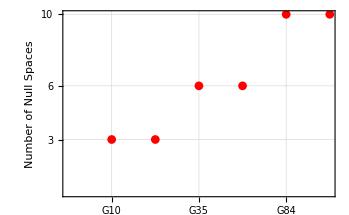

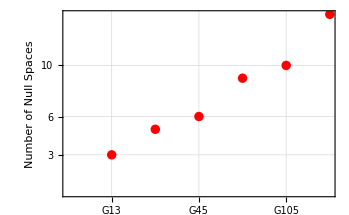

```mathematica
(*number of null spaces ordered as per the number of tensors*)
PlotDataFull=Table[{ii,NumNullSpacesFull⟦ii⟧},{ii,1,Length[NamesFullTheories]}];
PlotDataOrdered=Table[{ii,NumNullSpacesOrdered⟦ii⟧},{ii,1,Length[NamesOrderedTheories]}];

TicksFullTheories =Table[{ii,NamesFullTheories⟦ii⟧},{ii,1,Length[NamesFullTheories]}];

TicksOrderedTheories = Table[{ii,NamesOrderedTheories⟦ii⟧},{ii,1,Length[NamesOrderedTheories]}];

ListPlot[PlotDataFull,Frame->True,FrameTicks->{{NumNullSpacesFull,None},{TicksFullTheories,None}},GridLines->Automatic,FrameLabel->{{Style["Number of Null Spaces",FontSize->12,Black],None},{None,None}},FrameTicksStyle->Directive[FontSize->14,Black],PlotMarkers->Automatic,PlotStyle->{Thick,Red}]

ListPlot[PlotDataOrdered,Frame->True,FrameTicks->{{NumNullSpacesOrdered,None},{TicksOrderedTheories,None}},GridLines->Automatic,FrameLabel->{{Style["Number of Null Spaces",FontSize->12,Black],None},{None,None}},FrameTicksStyle->{{Directive[FontSize->14,Black],None},{Directive[FontSize->14,{Orange,Black}],None}},PlotStyle->{Thick,Red}]
```

```mathematica
TicksFullTheories
```

```mathematica
{{1,G10},{2,G20},{3,G35},{4,G56},{5,G84},{6,G120}}
```